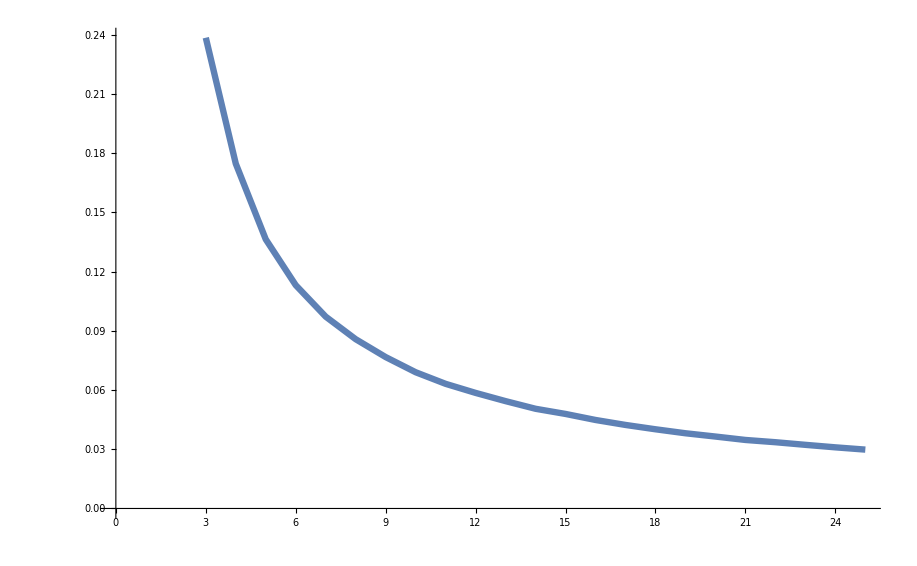

0.70099/x

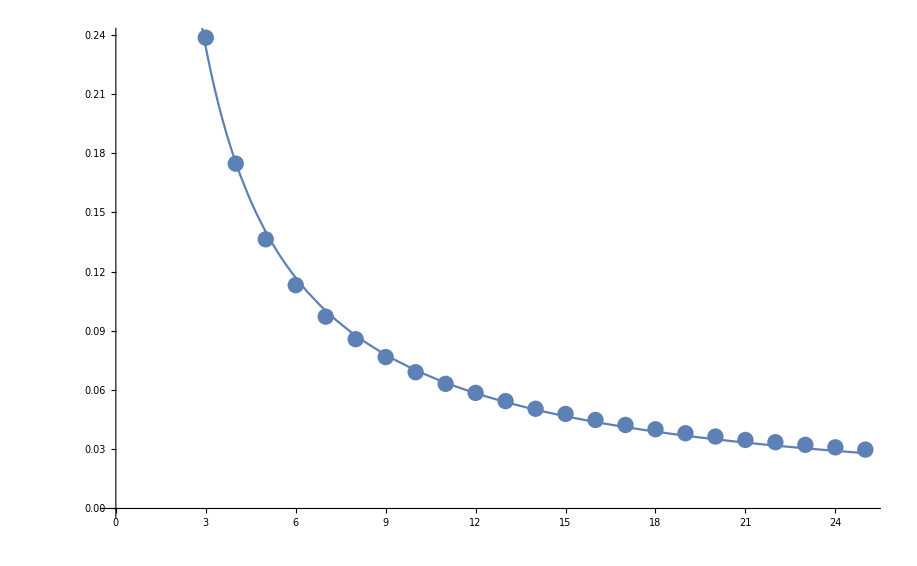

```mathematica
(*dataA10 = {0.069028, 0.123394, 0.103740, 0.102514, 0.101329, 0.101153, 0.102543,0.104086,  0.122916, 0.069298};
dataB10 = {0.069493, 0.123127, 0.103624, 0.102474, 0.100929, 0.101875, 0.102196, 0.103620, 0.123409, 0.069252};*)
data = {{3, 0.238513}, {4, 0.174703}, {5, 0.136372}, {6, 0.113139}, {7, 0.097183}, {8, 0.085763}, {9, 0.076707}, {10, 0.069028}, {11, 0.063145}, {12, 0.058554}, {13, 0.054385}, {14, 0.050511}, {15, 0.047895}, {16, 0.044840}, {17, 0.042321}, {18, 0.040125}, {19, 0.038108}, {20, 0.036445}, {21, 0.034716}, {22, 0.033573}, {23, 0.032244}, {24, 0.030975}, {25, 0.029825}};
xx = ListPlot[data, Joined -> True, PlotStyle -> {Thickness[0.005], Thickness[0.005]}, AxesStyle -> {Directive[Black, 22], Directive[Black, 22]}]
xx2 = ListPlot[data, PlotStyle -> {Thickness[0.005], Thickness[0.005]}, AxesStyle -> {Directive[Black, 22], Directive[Black, 22]}];
curve = Fit[data, {1/x}, x]
yy = Plot[1/(x), {x, 2, 25}];
zz = Plot[curve, {x, 1, 25}];
Show[xx2, zz]
```